```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
transeries=Transpose[series];
transeries=Drop[transeries,1];
Dimensions[transeries]
hopdates=Drop[series[[1]],4]
%//Length
countriescsv=transeries[[1]];
%//Dimensions
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

{120,267}

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20,4/19/20,4/20/20,4/21/20,4/22/20,4/23/20,4/24/20,4/25/20,4/26/20,4/27/20,4/28/20,4/29/20,4/30/20,5/1/20,5/2/20,5/3/20,5/4/20,5/5/20,5/6/20,5/7/20,5/8/20,5/9/20,5/10/20,5/11/20,5/12/20,5/13/20,5/14/20,5/15/20,5/16/20,5/17/20}

117

{267}

```mathematica
TableForm[series];
```

```mathematica
TableForm[s];
```

```mathematica
CountryData["Japan","Population"]
```

126225259

```mathematica
{"Singapore",200,{2.835279843883035*^8,64.38918662693713,0.1259411788554341},21,7,10,0},
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0},
```

```mathematica
countryparameters=
(*name,truncdrop,jp0,lag,projtime,bootlag,plotdrop*)
{
{"Spain",300,{220179.72743729973,3738.260142762334,0.140854450046756},35,21,3,0},{"Canada",200,{81077.39354813701,1942.4785517808518,0.09614986026664779},21,21,10,0},{"Australia",100,{6739.694777539763,109.80989304529129,0.2176890747257849},35,21,3,0},{"New Zealand",5,{1474.4790552718507,17.837297202136803,0.22787919159710443},21,21,10,0},{"Croatia",10,{2136.3445533928943,31.72191300732455,0.14074152304198262},42,21,2,0},{"Czechia",10,{7901.635972368201,127.858460333728,0.13557437401035852},28,21,5,0},{"Sweden",200,{31272.793301689162,709.071763360148,0.08355406779130738},28,21,10,0},{"Greece",50,{2666.2946598125536,129.93576587902731,0.11994181591439824},28,21,10,0},{"Japan",950,{16302.099406766767,451.80679351636303,0.1327048660761382},28,21,8,0},{"Denmark",1100,{10976.989187588755,1103.472360444931,0.09290172311994832},28,21,10,0},{"Russia",300,{369442.4708046471,1404.1124969291448,0.114562446419243},21,21,10,0},{"United Kingdom",200,{242613.6018213363,2637.774825046479,0.10113748577252618},21,14,10,0},{"Hungary",50,{3497.602134723886,112.69091970270172,0.10969692792738958},35,21,5,0},{"France",300,{177843.2636752088,1554.9147679208638,0.1371138414227038},35,21,5,0},{"Singapore",900,{26421.784728354156,555.472525673107,0.1403556555382898},28,21,5,0},{"Serbia",50,{10410.396290570648,127.16306680915262,0.13621047340777273},28,21,5,0},{"Poland",50,{17709.029565845885,459.31825489863706,0.09649995071438171},35,21,5,0}
}
```

{{Spain,300,{220180.,3738.26,0.140854},35,21,3,0},{Canada,200,{81077.4,1942.48,0.0961499},21,21,10,0},{Australia,100,{6739.69,109.81,0.217689},35,21,3,0},{New Zealand,5,{1474.48,17.8373,0.227879},21,21,10,0},{Croatia,10,{2136.34,31.7219,0.140742},42,21,2,0},{Czechia,10,{7901.64,127.858,0.135574},28,21,5,0},{Sweden,200,{31272.8,709.072,0.0835541},28,21,10,0},{Greece,50,{2666.29,129.936,0.119942},28,21,10,0},{Japan,950,{16302.1,451.807,0.132705},28,21,8,0},{Denmark,1100,{10977.,1103.47,0.0929017},28,21,10,0},{Russia,300,{369442.,1404.11,0.114562},21,21,10,0},{United Kingdom,200,{242614.,2637.77,0.101137},21,14,10,0},{Hungary,50,{3497.6,112.691,0.109697},35,21,5,0},{France,300,{177843.,1554.91,0.137114},35,21,5,0},{Singapore,900,{26421.8,555.473,0.140356},28,21,5,0},{Serbia,50,{10410.4,127.163,0.13621},28,21,5,0},{Poland,50,{17709.,459.318,0.0965},35,21,5,0}}

```mathematica
Export["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml",countryparameters]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml

```mathematica
countryparameters=Import["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml"]
```

{{Spain,300,{220180.,3738.26,0.140854},35,21,3,0},{Canada,200,{81077.4,1942.48,0.0961499},21,21,10,0},{Australia,100,{6739.69,109.81,0.217689},35,21,3,0},{New Zealand,5,{1474.48,17.8373,0.227879},21,21,10,0},{Croatia,10,{2136.34,31.7219,0.140742},35,21,3,0},{Czechia,10,{7901.64,127.858,0.135574},21,21,10,0},{Sweden,200,{31272.8,709.072,0.0835541},28,21,10,0},{Greece,50,{2666.29,129.936,0.119942},28,21,10,0},{Japan,950,{16302.1,451.807,0.132705},28,21,8,0},{Denmark,1100,{10977.,1103.47,0.0929017},28,21,10,0},{Russia,300,{369442.,1404.11,0.114562},21,21,10,0},{United Kingdom,200,{242614.,2637.77,0.101137},21,14,10,0},{Hungary,50,{3497.6,112.691,0.109697},28,21,10,0},{France,300,{177843.,1554.91,0.137114},28,21,10,0},{Singapore,900,{26421.8,555.473,0.140356},28,21,5,0},{Serbia,50,{10410.4,127.163,0.13621},28,21,5,0},{Poland,50,{17709.,459.318,0.0965},21,21,5,0}}

```mathematica
"Spain",
```

```mathematica
wolfcountrynames={"Spain","Canada","Australia","New Zealand","Croatia","CzechRepublic","Sweden","Greece","Japan","Denmark","Russia","United Kingdom","Hungary","France","Singapore","Serbia","Poland"};
wpopulations=Map[CountryData[#,"Population"][[1]]&,wolfcountrynames]
lesscountrynames={};
morecountrynames={};
countrybootabcs={};
lesscountrybootabcs={};
morecountrybootabcs={};
```

{47290504,35309555,23502754,4554858,4369961,10611300,9595619,11470255,126225259,5628958,142400066,63556184,9918377,64101308,5336859,7164132,38344752}

```mathematica
lesscountrybootabcs={};
morecountrybootabcs={};
```

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump

country : Spain

data length : 73

start date : {2020,3,6}

jdp0 : {222467.,3999.44,0.137719}

jp20 : {231524.,17492.3,0.09214}

backward result : {167614.,1112.46,0.204769}

forward result : {231524.,17492.3,0.09214}

last tab: {231524.,17492.3,0.09214}

backward result : {167614.,1112.46,0.204769}

forward result : {231524.,17492.3,0.09214}

past errors : {{4332.03,4587.22,4352.54},4423.93}

boot tab : {{186530.,1671.28,0.181892},{187643.,1734.65,0.180021},{187518.,1756.37,0.179529},{191076.,1928.78,0.174693},{198952.,2325.26,0.165049},{207497.,2795.91,0.155639},{209014.,2950.5,0.153195},{216284.,3472.56,0.145281},{216699.,3624.45,0.143609},{221148.,4085.88,0.138205},{225033.,4593.68,0.133151},{231109.,5360.53,0.126413},{218913.,4457.09,0.135966},{217711.,4551.12,0.135695},{215925.,4620.65,0.135852},{217815.,5156.48,0.131712},{219229.,5774.,0.127701},{220940.,6428.91,0.123795},{221325.,6831.31,0.121842},{222424.,7393.35,0.119085},{223254.,7932.51,0.116714},{224065.,8563.09,0.114206},{224404.,9054.78,0.112508},{225123.,9681.48,0.110345},{225606.,10131.,0.108892},{226190.,10507.1,0.107628},{226938.,10913.7,0.106238},{227229.,10894.9,0.106106},{227598.,10988.5,0.105662},{229952.,13132.6,0.0998485},{231281.,14892.5,0.095989},{232597.,16844.2,0.092229},{233612.,18950.8,0.0888058},{234642.,21594.7,0.0850998},{235778.,25128.7,0.0808666},{236538.,29180.1,0.0769483}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73}

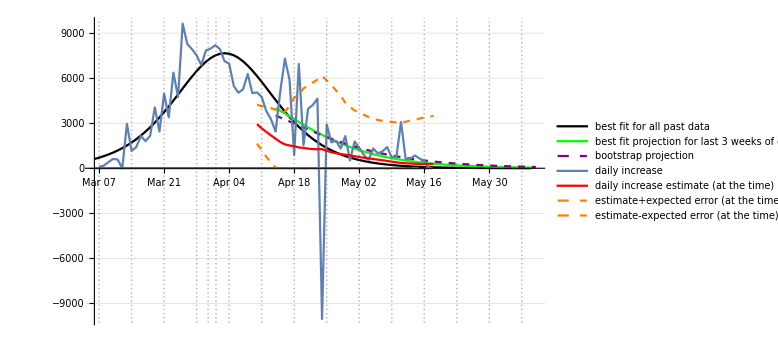

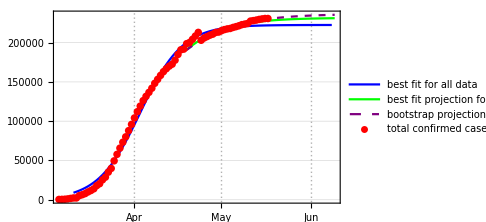

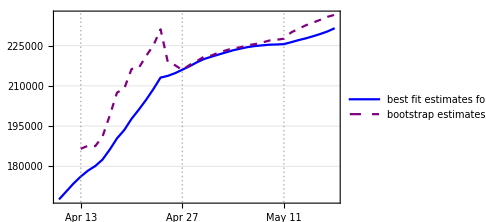

May 17

Spaindate.txt

Spaingraf.png

Spainloggraf.png

Spaindfgraf.png

Spainfinalplot.png

country : Canada

data length : 64

start date : {2020,3,15}

jdp0 : {84065.4,2087.07,0.0929371}

jp20 : {91298.1,3097.95,0.0798843}

backward result : {19758.,271.885,0.236761}

forward result : {91298.1,3097.95,0.0798843}

last tab: {91298.1,3097.95,0.0798843}

backward result : {19758.,271.885,0.236761}

forward result : {91298.1,3097.95,0.0798843}

past errors : {{-67.8402,-269.111,-497.983,-681.947,-837.813,-952.699,-956.017,-946.456,-819.967,-766.739},-679.657}

boot tab : {{45964.5,1055.02,0.134761},{40413.3,945.381,0.143646},{47860.2,1228.25,0.127227},{57820.1,1589.,0.11208},{69248.4,1966.04,0.100292},{78777.9,2323.85,0.0919712},{96797.7,2733.85,0.0835396},{120684.,3157.66,0.0764033},{182039.,3637.78,0.0690106},{230772.,3965.05,0.0651527},{261492.,4221.32,0.0627344},{299529.,4547.98,0.0600505},{209723.,4506.01,0.0616834},{159262.,4447.61,0.0636705},{127431.,4244.93,0.0669304},{112896.,4043.81,0.0697297},{98394.2,3644.62,0.0746826},{91246.,3302.05,0.0788237},{82101.6,2696.91,0.0867844},{85957.5,2949.36,0.0832405},{87589.7,3136.47,0.081158},{87765.,3217.67,0.0804896},{96638.7,4195.26,0.0715204},{102280.,4767.31,0.06718},{107052.,5223.16,0.0640765},{108655.,5479.49,0.0626711},{111805.,5974.59,0.0601418},{111109.,6113.17,0.0597657},{110049.,6202.6,0.0596625},{100472.,5043.63,0.0664235},{95181.1,4127.04,0.0723865},{92363.3,3474.95,0.0770842},{90311.4,2908.93,0.0816808},{90130.3,2767.56,0.0827593}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64}

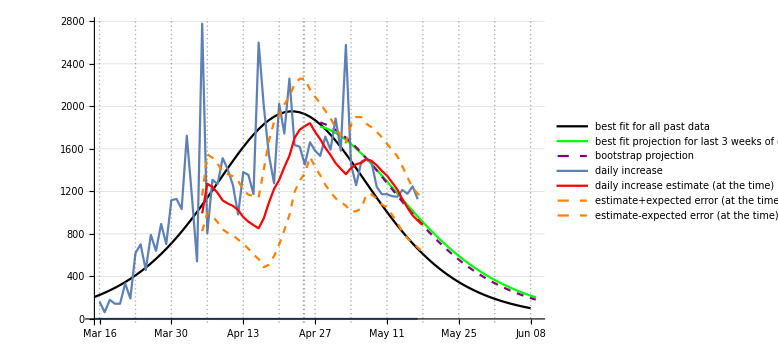

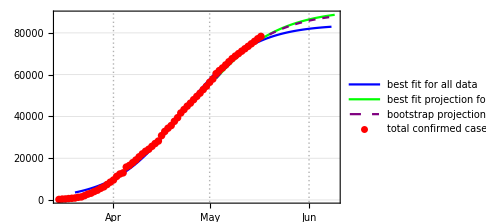

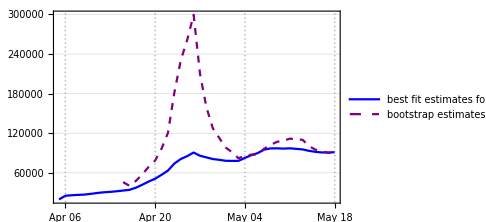

May 17

Canadadate.txt

Canadagraf.png

Canadaloggraf.png

Canadadfgraf.png

Canadafinalplot.png

country : Australia

data length : 69

start date : {2020,3,10}

jdp0 : {6776.62,115.145,0.214501}

jp20 : {7453.72,5050.96,0.0304433}

backward result : {6368.94,71.507,0.247471}

forward result : {7453.72,5050.96,0.0304433}

last tab: {7453.72,5050.96,0.0304433}

backward result : {6368.94,71.507,0.247471}

forward result : {7453.72,5050.96,0.0304433}

past errors : {{40.8357,40.8817,42.3197},41.3457}

boot tab : {{6496.8,81.6966,0.237981},{6521.69,84.1447,0.235941},{6546.87,86.8701,0.233777},{6574.75,90.3892,0.231163},{6588.08,92.7787,0.229553},{6602.95,96.2065,0.22741},{6610.94,99.6007,0.225517},{6622.21,105.338,0.222532},{6638.71,116.156,0.217465},{6656.47,129.003,0.212099},{6666.67,133.321,0.210305},{6680.88,149.383,0.204784},{6699.85,170.84,0.198314},{6720.58,206.309,0.189577},{6739.29,246.03,0.181602},{6762.29,317.459,0.170438},{6781.13,381.096,0.162489},{6803.99,473.427,0.153174},{6823.81,558.839,0.146029},{6860.98,786.09,0.131631},{6897.65,1078.08,0.11819},{6940.51,1472.5,0.104447},{6972.62,1875.02,0.0936385},{7010.18,2278.4,0.0840932},{7042.47,2675.75,0.0759352},{7109.15,3287.18,0.0639075},{7190.88,3901.05,0.0524118},{7284.69,4392.97,0.0429723},{7488.57,4902.13,0.0316154},{7650.6,5143.45,0.0259021},{7680.84,5206.36,0.0247037},{7739.47,5309.96,0.0226972}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69}

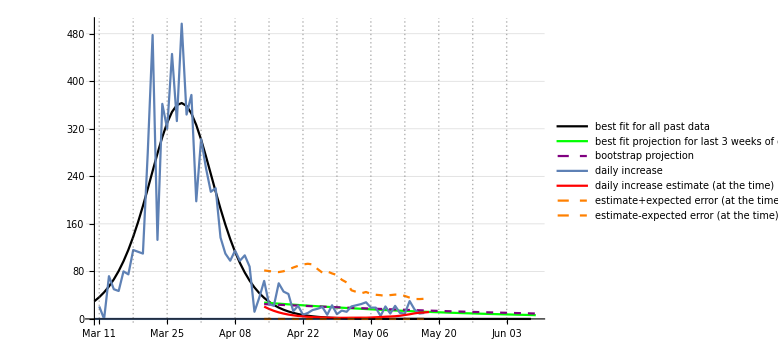

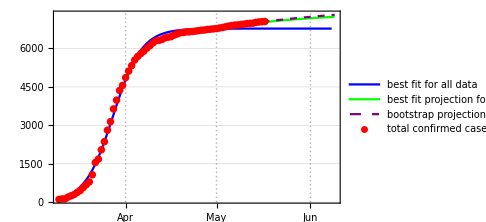

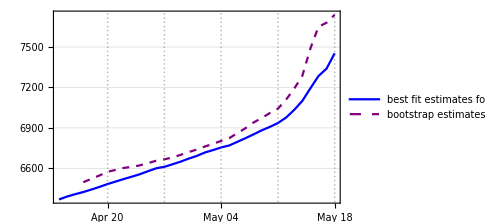

May 17

Australiadate.txt

Australiagraf.png

Australialoggraf.png

Australiadfgraf.png

Australiafinalplot.png

country : New Zealand

data length : 65

start date : {2020,3,14}

jdp0 : {1477.75,18.1725,0.226658}

jp20 : {1503.79,505.811,0.1001}

backward result : {981.19,4.49853,0.341492}

forward result : {1503.79,505.811,0.1001}

last tab: {1503.79,505.811,0.1001}

backward result : {981.19,4.49853,0.341492}

forward result : {1503.79,505.811,0.1001}

past errors : {{1.23498,2.5777,5.00345,4.5018,4.0636,3.68086,4.34658,4.05465,4.79972,4.5771},3.88404}

boot tab : {{1833.01,53.1616,0.158085},{1745.34,52.5281,0.161741},{1653.58,49.0838,0.169019},{1584.85,44.396,0.177548},{1536.2,38.8581,0.18697},{1509.47,34.2446,0.194769},{1500.49,32.6958,0.197606},{1488.29,29.0462,0.2039},{1478.53,26.5983,0.208752},{1482.16,31.3381,0.201653},{1481.68,34.8448,0.197617},{1486.04,47.1765,0.185404},{1494.82,73.9462,0.167186},{1492.82,86.0635,0.162189},{1499.51,118.295,0.149442},{1507.24,167.934,0.135325},{1512.91,217.538,0.124841},{1526.04,352.045,0.104276},{1541.97,501.305,0.0868885},{1541.36,548.281,0.0833017},{1538.38,595.871,0.0804977},{1525.29,553.665,0.0871638},{1515.9,524.223,0.0925596},{1510.22,485.594,0.0978167},{1505.99,427.729,0.104363},{1507.1,518.11,0.0971671},{1511.13,670.673,0.0851263},{1514.37,798.974,0.075802},{1511.75,779.767,0.0783427},{1512.5,869.343,0.0727382},{1512.13,923.672,0.0698722},{1517.09,1089.67,0.0568345},{1515.11,1105.19,0.057061},{1512.17,993.037,0.0658872},{1511.98,1007.32,0.0652468}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}

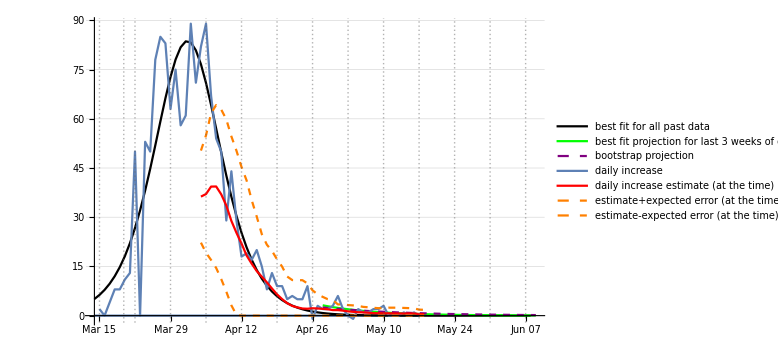

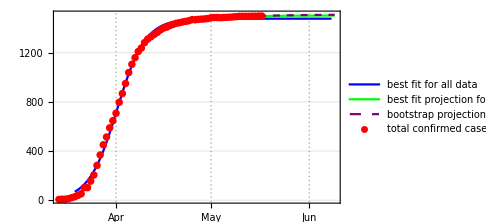

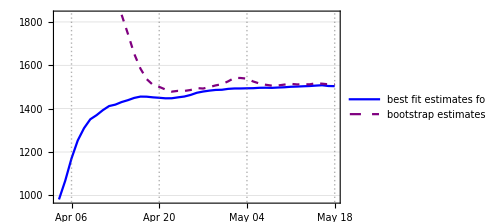

May 17

newzealanddate.txt

newzealandgraf.png

newzealandloggraf.png

newzealanddfgraf.png

newzealandfinalplot.png

country : Croatia

data length : 73

start date : {2020,3,6}

jdp0 : {2157.,33.7907,0.137918}

jp20 : {2215.5,85.5438,0.10852}

backward result : {1844.39,16.1435,0.173991}

forward result : {2215.5,85.5438,0.10852}

last tab: {2215.5,85.5438,0.10852}

backward result : {1844.39,16.1435,0.173991}

forward result : {2215.5,85.5438,0.10852}

past errors : {{37.6143,37.5457},37.58}

boot tab : {{1972.08,20.8496,0.160684},{1990.2,21.7632,0.158586},{1989.4,21.9314,0.158313},{1997.43,22.5204,0.157114},{2026.73,24.2083,0.153671},{2052.81,25.948,0.150465},{2073.67,27.568,0.147748},{2078.51,28.4123,0.146575},{2084.14,29.4274,0.145223},{2089.63,30.6318,0.143726},{2094.82,32.1021,0.142037},{2105.07,34.3334,0.139539},{2117.1,37.1727,0.136615},{2127.45,40.5175,0.133575},{2131.6,42.9261,0.131658},{2137.06,45.7621,0.129522},{2141.76,48.5592,0.127575},{2148.04,51.5578,0.125564},{2153.58,54.6634,0.123643},{2158.86,58.3868,0.12154},{2175.82,64.2113,0.118125},{2188.97,69.5862,0.115316},{2199.01,75.4458,0.112658},{2207.17,80.831,0.110428},{2215.19,86.0879,0.108377},{2218.47,86.793,0.107992},{2223.41,89.6489,0.106899},{2225.34,90.265,0.106613},{2227.8,92.9695,0.105736},{2231.17,97.6473,0.104336}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73}

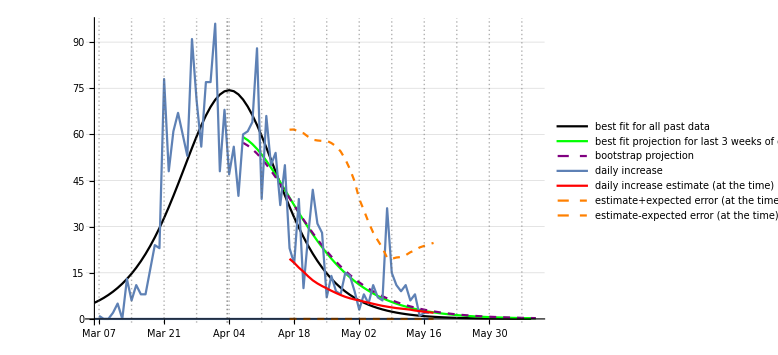

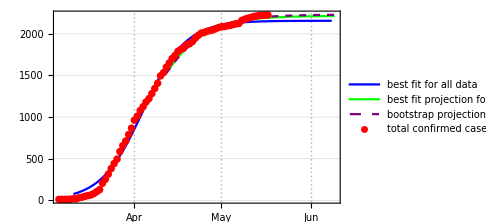

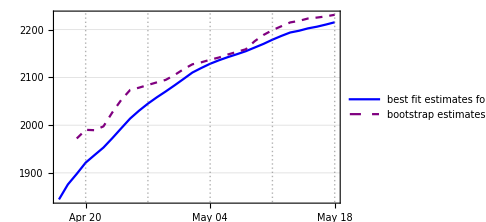

May 17

Croatiadate.txt

Croatiagraf.png

Croatialoggraf.png

Croatiadfgraf.png

Croatiafinalplot.png

country : Czechia

data length : 74

start date : {2020,3,5}

jdp0 : {8030.96,142.386,0.130841}

jp20 : {9529.55,2857.21,0.0393301}

backward result : {4764.4,22.8466,0.22743}

forward result : {9529.55,2857.21,0.0393301}

last tab: {9529.55,2857.21,0.0393301}

backward result : {4764.4,22.8466,0.22743}

forward result : {9529.55,2857.21,0.0393301}

past errors : {{67.2698,124.865,157.133,184.967,185.267},143.9}

boot tab : {{6689.38,49.6665,0.18026},{6634.18,50.3645,0.179912},{6985.18,58.2088,0.172082},{7072.76,62.5466,0.168676},{7236.33,68.5592,0.164177},{7181.1,69.4993,0.163944},{7274.92,74.5423,0.160748},{7095.86,71.4564,0.163461},{6874.56,65.3971,0.168358},{6810.09,65.0244,0.169133},{6975.74,74.4212,0.162872},{7038.37,79.6629,0.159926},{7064.62,82.7677,0.158364},{7241.18,98.6307,0.150839},{7477.7,126.377,0.140626},{7690.78,162.179,0.130879},{7876.44,203.357,0.122345},{8019.85,246.683,0.115367},{8158.43,292.086,0.109269},{8209.75,319.164,0.106263},{8196.39,339.842,0.104573},{8180.92,369.722,0.102362},{8203.18,409.969,0.099329},{8308.58,501.629,0.0929274},{8499.86,636.929,0.0848808},{8632.95,772.971,0.0786929},{8574.32,777.446,0.0790439},{8581.45,848.361,0.0767766},{8564.14,901.679,0.0754316},{8654.03,1055.61,0.0706534},{8716.44,1156.41,0.0678018},{8766.18,1201.97,0.0663645},{8759.06,1174.16,0.0669768},{8700.17,1095.86,0.0692065},{8608.58,938.575,0.0737928},{8619.42,938.659,0.0736381},{8697.13,1101.64,0.0691197},{8856.7,1461.51,0.0609469},{9198.51,2048.27,0.0498129},{9717.04,2748.52,0.0389822},{10850.7,3640.89,0.0269475},{11753.1,4082.27,0.0217244}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74}

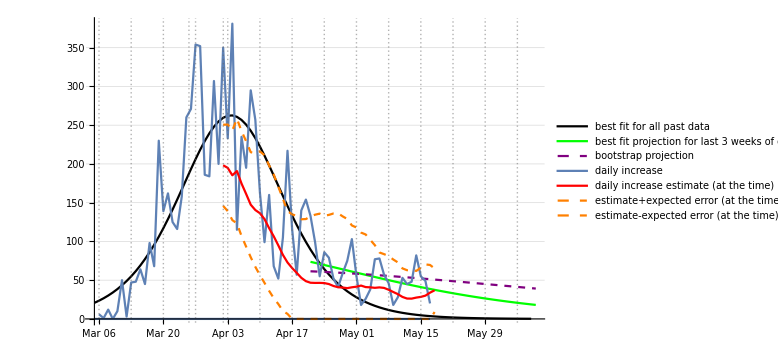

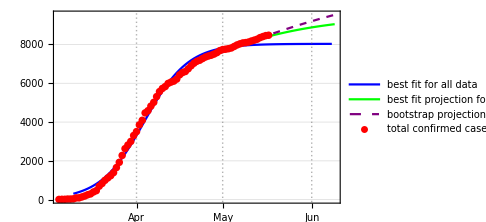

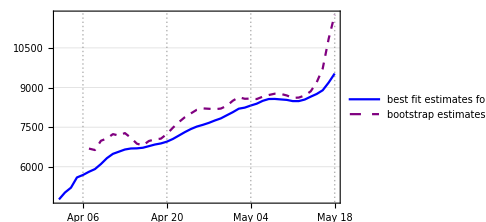

May 17

Czechiadate.txt

Czechiagraf.png

Czechialoggraf.png

Czechiadfgraf.png

Czechiafinalplot.png

country : Sweden

data length : 71

start date : {2020,3,8}

jdp0 : {33375.9,794.148,0.0791364}

jp20 : {43044.5,2096.11,0.0536221}

backward result : {33816.,391.165,0.107741}

forward result : {43044.5,2096.11,0.0536221}

last tab: {43044.5,2096.11,0.0536221}

backward result : {33816.,391.165,0.107741}

forward result : {43044.5,2096.11,0.0536221}

past errors : {{376.849,591.303,567.016,506.142,715.74,976.783,1290.17,1571.71,1714.18,1868.27},1017.82}

boot tab : {{14328.6,230.525,0.14094},{15189.8,252.891,0.1354},{16812.4,298.978,0.126058},{18482.6,343.08,0.118537},{18921.5,352.548,0.116978},{18681.,340.621,0.118503},{18698.9,343.557,0.118173},{19793.6,391.331,0.112252},{22360.6,500.522,0.101305},{25768.5,630.977,0.0912165},{30601.6,789.143,0.081737},{35234.9,926.372,0.0752642},{38271.4,1035.56,0.071228},{37837.5,1089.33,0.0700247},{40186.1,1191.01,0.0670223},{42912.6,1301.13,0.0640638},{48101.9,1437.3,0.060466},{47961.8,1484.1,0.0597095},{48083.6,1540.1,0.0588103},{42991.7,1484.04,0.0609178},{38885.9,1401.71,0.0636298},{36574.1,1342.79,0.0656413},{36353.8,1351.17,0.0656313},{37506.4,1420.1,0.0639629},{37944.7,1449.12,0.0633038},{38539.4,1494.78,0.0623435},{37550.9,1453.47,0.0634232},{37142.7,1448.16,0.0637244},{38093.,1559.2,0.0616907},{41026.8,1855.19,0.0567605},{45412.1,2242.55,0.0513302},{50337.3,2615.71,0.0469144},{53198.,2854.46,0.0445761},{55237.1,3055.39,0.0428722}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71}

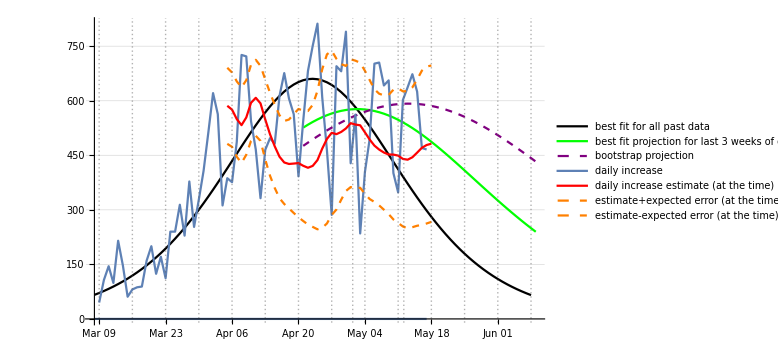

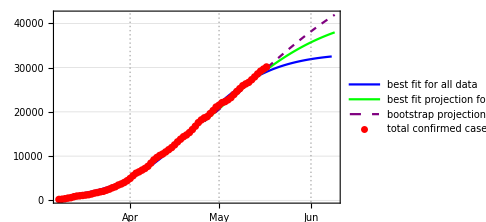

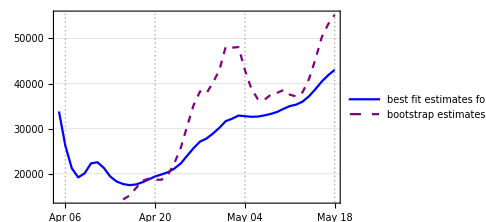

May 17

Swedendate.txt

Swedengraf.png

Swedenloggraf.png

Swedendfgraf.png

Swedenfinalplot.png

country : Greece

data length : 71

start date : {2020,3,8}

jdp0 : {2703.57,138.041,0.116295}

jp20 : {2927.62,606.373,0.0622803}

backward result : {2478.4,89.1455,0.143581}

forward result : {2927.62,606.373,0.0622803}

last tab: {2927.62,606.373,0.0622803}

backward result : {2478.4,89.1455,0.143581}

forward result : {2927.62,606.373,0.0622803}

past errors : {{-16.5966,-10.5709,-16.931,-18.7002,-11.9017,-6.55818,-6.69192,23.6752,23.522,29.8276},-1.09257}

boot tab : {{2352.44,85.4084,0.14789},{2343.2,82.2574,0.149785},{2378.88,87.4267,0.14601},{2379.53,86.5441,0.146415},{2374.13,85.708,0.147053},{2332.45,75.2657,0.15395},{2313.2,68.0001,0.158783},{2460.69,105.336,0.135574},{2480.71,114.594,0.131611},{2574.66,155.517,0.116975},{2663.68,207.482,0.103821},{2751.31,268.599,0.0923139},{2831.38,333.203,0.0829139},{2981.54,446.152,0.0698082},{3254.89,597.533,0.0555793},{3545.4,723.148,0.0460135},{3813.47,804.55,0.0403635},{3858.77,851.617,0.0382303},{3782.99,876.723,0.0378806},{3567.73,866.674,0.0401119},{3425.27,878.147,0.0412799},{3283.76,864.802,0.043684},{3251.32,891.749,0.0432673},{3125.08,838.777,0.0474699},{2993.31,729.365,0.054813},{2911.73,596.623,0.0630439},{2853.22,461.868,0.0721111},{2816.19,344.216,0.0811597},{2810.11,285.828,0.085819},{2815.67,256.654,0.0878688},{2810.39,211.809,0.0924258},{2882.19,377.658,0.0752766},{2915.85,495.079,0.0674071},{3060.,957.534,0.0455555}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71}

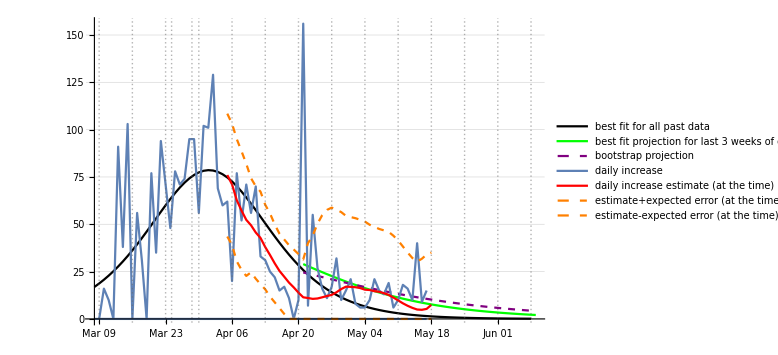

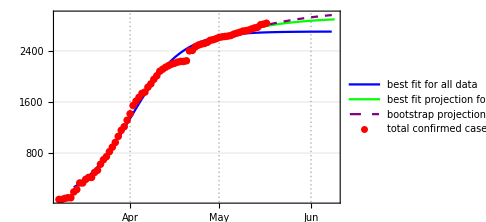

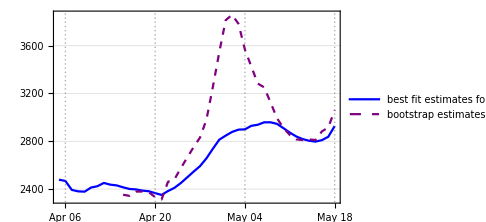

May 17

Greecedate.txt

Greecegraf.png

Greeceloggraf.png

Greecedfgraf.png

Greecefinalplot.png

country : Japan

data length : 59

start date : {2020,3,20}

jdp0 : {16378.8,460.926,0.131637}

jp20 : {16508.1,641.325,0.121288}

backward result : {61680.7,682.989,0.0970644}

forward result : {16508.1,641.325,0.121288}

last tab: {16508.1,641.325,0.121288}

backward result : {61680.7,682.989,0.0970644}

forward result : {16508.1,641.325,0.121288}

past errors : {{167.814,178.685,247.733,283.129,314.128,362.065,365.349,386.454},288.17}

boot tab : {{13315.9,224.523,0.172372},{12884.9,183.951,0.183025},{12913.8,169.381,0.18627},{13895.7,210.611,0.172145},{14183.,221.253,0.168669},{14778.9,252.027,0.160776},{15213.8,273.627,0.155685},{15185.2,264.216,0.157101},{15204.2,253.168,0.158499},{15385.7,269.733,0.155293},{15572.8,286.889,0.152121},{15510.1,281.065,0.153143},{15673.4,313.075,0.148617},{16104.5,415.583,0.136944},{16354.4,485.623,0.130597},{16549.8,566.312,0.124749},{16728.6,644.714,0.119783},{16719.7,656.461,0.119278},{16854.1,778.881,0.113478},{16953.4,944.556,0.107381},{17125.5,1234.12,0.0988339},{17087.5,1245.1,0.0988276},{17019.8,1199.61,0.100298},{16943.3,1094.82,0.103285}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59}

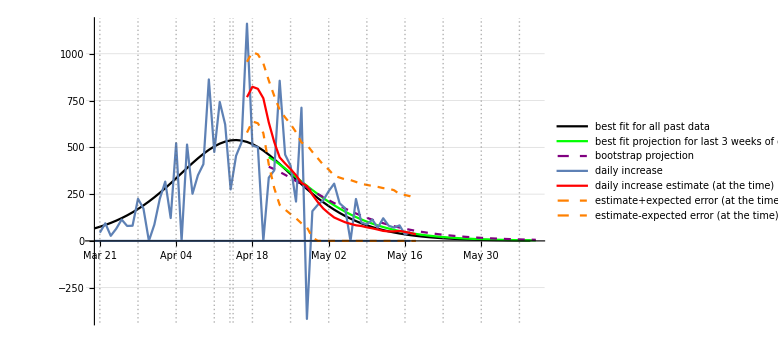

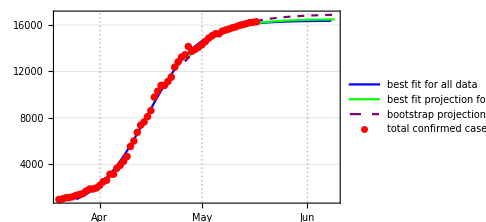

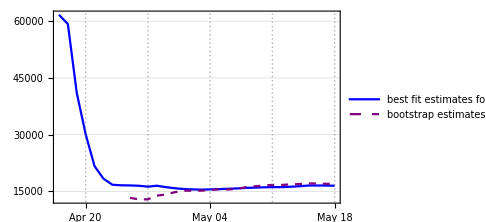

May 17

Japandate.txt

Japangraf.png

Japanloggraf.png

Japandfgraf.png

Japanfinalplot.png

country : Denmark

data length : 61

start date : {2020,3,18}

jdp0 : {11208.9,1146.03,0.0897835}

jp20 : {12416.6,2038.22,0.0624918}

backward result : {9622.11,847.804,0.116597}

forward result : {12416.6,2038.22,0.0624918}

last tab: {12416.6,2038.22,0.0624918}

backward result : {9622.11,847.804,0.116597}

forward result : {12416.6,2038.22,0.0624918}

past errors : {{40.6576,29.3994,30.8449,9.96764,-13.2676,-34.9041,-82.9926,-95.5903,-115.76,-130.571},-36.2216}

boot tab : {{8789.2,690.271,0.132732},{9408.77,861.385,0.115934},{9904.5,1019.76,0.104163},{10433.3,1208.42,0.0930967},{11116.9,1440.04,0.0818724},{12051.9,1723.91,0.0705372},{13311.5,2038.43,0.0600674},{14942.3,2343.1,0.0513308},{16294.8,2588.,0.0456477},{18136.9,2839.26,0.0403361},{21170.9,3096.81,0.035147},{23245.4,3265.43,0.0323379},{22570.4,3327.2,0.0320358},{21830.8,3367.96,0.0320182},{20732.4,3388.28,0.0324607},{18584.,3330.68,0.0346045},{16820.3,3229.62,0.0374526},{15384.5,3089.32,0.0410211},{14363.4,2912.09,0.0450017},{13624.2,2711.42,0.0492465},{12879.6,2385.73,0.0558036},{12512.6,2138.64,0.060687},{12309.8,1951.14,0.0643636},{12177.5,1804.97,0.0672895}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61}

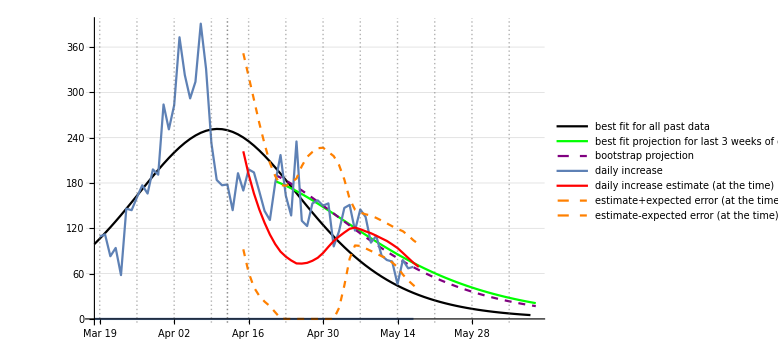

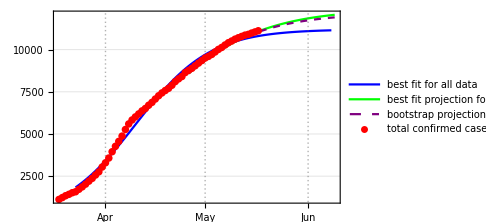

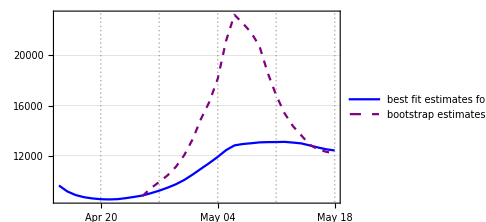

May 17

Denmarkdate.txt

Denmarkgraf.png

Denmarkloggraf.png

Denmarkdfgraf.png

Denmarkfinalplot.png

country : Russia

data length : 58

start date : {2020,3,21}

jdp0 : {386549.,1499.91,0.112329}

jp20 : {408456.,1771.14,0.107606}

backward result : {40899.,291.658,0.19182}

forward result : {408456.,1771.14,0.107606}

last tab: {408456.,1771.14,0.107606}

backward result : {40899.,291.658,0.19182}

forward result : {408456.,1771.14,0.107606}

past errors : {{474.281,-25.0158,-517.036,-500.544,-1321.75,-3038.31,-4776.42,-5801.9,-8082.25,-9658.69},-3324.76}

boot tab : {{339753.,540.719,0.148964},{272232.,541.224,0.149824},{216291.,537.8,0.151313},{166931.,488.092,0.156903},{148516.,426.755,0.163075},{133704.,340.318,0.172608},{134487.,325.5,0.174075},{134147.,304.939,0.176344},{130117.,251.508,0.183418},{113530.,111.805,0.213888},{132929.,236.39,0.184824},{153795.,406.755,0.164158},{195097.,798.069,0.139122},{277844.,1473.14,0.116604},{402294.,2168.37,0.102661},{589601.,2844.32,0.0932146},{866125.,3450.89,0.0867415},{1.33778×10^6,4007.18,0.0818926},{1.85067×10^6,4459.32,0.0787167},{2.04861×10^6,4727.18,0.077201},{1.71019×10^6,4795.62,0.0771761},{1.4578×10^6,4860.79,0.0772081},{1.12311×10^6,4809.04,0.078158},{820690.,4491.48,0.0809398},{621510.,3848.,0.0860709},{509416.,3038.66,0.0930349},{435803.,2179.88,0.102168},{391270.,1453.56,0.112624}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58}

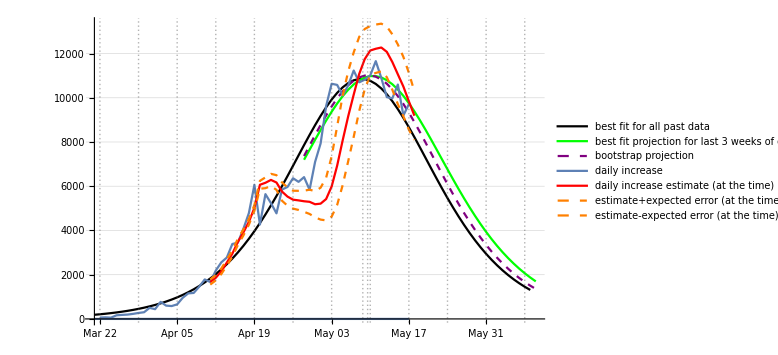

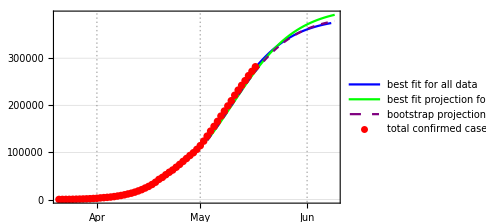

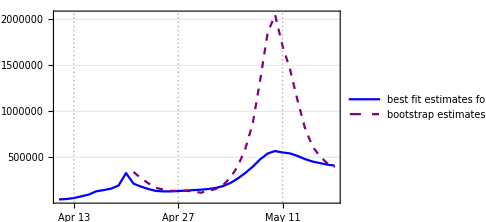

May 17

Russiadate.txt

Russiagraf.png

Russialoggraf.png

Russiadfgraf.png

Russiafinalplot.png

country : United Kingdom

data length : 72

start date : {2020,3,7}

jdp0 : {254562.,3051.43,0.09623}

jp20 : {295068.,7489.64,0.0726358}

backward result : {109233.,204.099,0.209633}

forward result : {295068.,7489.64,0.0726358}

last tab: {295068.,7489.64,0.0726358}

backward result : {109233.,204.099,0.209633}

forward result : {295068.,7489.64,0.0726358}

past errors : {{1272.85,632.23,95.6586,-400.3,-1283.56,-2240.53,-2891.12,-3333.74,-3781.29,-4047.18},-1597.7}

boot tab : {{83241.9,195.501,0.211712},{78715.9,169.211,0.218966},{104119.,386.441,0.179579},{124173.,562.919,0.162089},{161690.,722.568,0.149431},{167872.,807.496,0.145055},{167177.,860.08,0.143001},{161292.,887.738,0.142526},{173543.,1053.12,0.13579},{164724.,1037.13,0.137269},{173159.,1212.29,0.131495},{191688.,1498.9,0.123273},{201406.,1708.79,0.1186},{216532.,2016.16,0.112684},{204744.,2024.87,0.113565},{199855.,2112.68,0.112913},{199191.,2256.34,0.111236},{206738.,2631.07,0.106331},{218142.,3158.27,0.100419},{233208.,3921.28,0.0935452},{245292.,4596.52,0.0886055},{256027.,5373.87,0.0839984},{266253.,6354.42,0.0792965},{271707.,7244.,0.0758797},{303860.,9479.33,0.0678445},{342853.,11586.,0.0616172},{384735.,13746.,0.0564606},{420258.,15595.3,0.0528094},{442573.,17236.6,0.0501939},{452556.,18487.3,0.0485367},{557306.,21804.8,0.0435262},{777099.,25866.8,0.0383125},{998570.,28707.5,0.0353624},{979455.,29777.3,0.0347381},{657178.,27447.,0.0380413},{507881.,24665.4,0.0419025},{418843.,21208.1,0.0467807},{370329.,17956.5,0.0516757},{343410.,15264.,0.0560629},{325565.,12751.1,0.0604977},{304074.,9099.11,0.0683173},{287128.,5766.03,0.078179}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72}

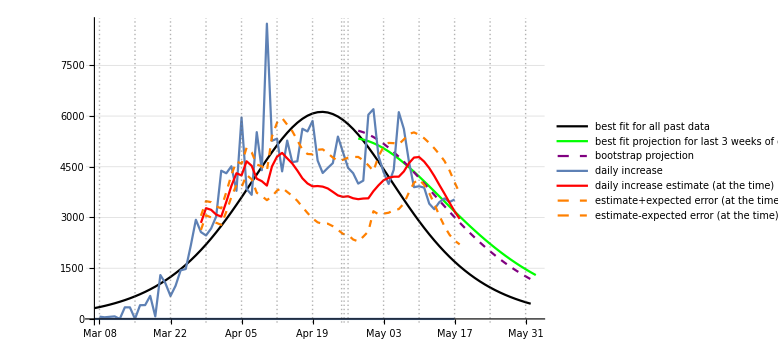

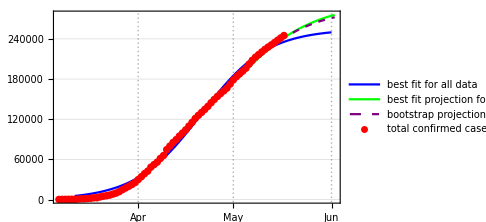

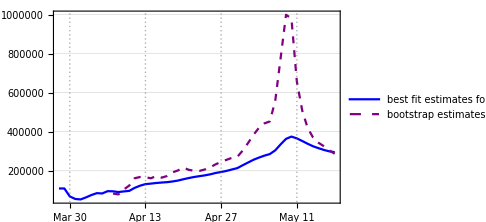

May 17

ukdate.txt

ukgraf.png

ukloggraf.png

ukdfgraf.png

ukfinalplot.png

country : Hungary

data length : 61

start date : {2020,3,18}

jdp0 : {3557.45,118.075,0.107269}

jp20 : {3679.99,171.951,0.0945008}

backward result : {2772.04,83.243,0.130272}

forward result : {3679.99,171.951,0.0945008}

last tab: {3679.99,171.951,0.0945008}

backward result : {2772.04,83.243,0.130272}

forward result : {3679.99,171.951,0.0945008}

past errors : {{3.83416,19.8553,35.7945,72.5145,90.8835},44.5764}

boot tab : {{3500.06,113.116,0.109929},{3566.22,116.977,0.108075},{3534.7,117.666,0.10812},{3455.03,115.993,0.109379},{3434.71,116.148,0.10954},{3541.95,123.412,0.106242},{3634.3,130.392,0.103378},{3671.69,133.633,0.102144},{3651.2,133.076,0.102478},{3626.13,131.664,0.103097},{3617.,131.958,0.103127},{3588.62,129.984,0.103948},{3557.62,127.865,0.104877},{3553.48,128.649,0.104752},{3590.83,135.489,0.10265},{3599.59,142.008,0.101168},{3622.92,152.15,0.0988498},{3651.59,165.181,0.0961093},{3701.65,185.2,0.0921779},{3720.37,191.133,0.0910128},{3766.81,201.254,0.0888611},{3788.55,203.681,0.088162}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61}

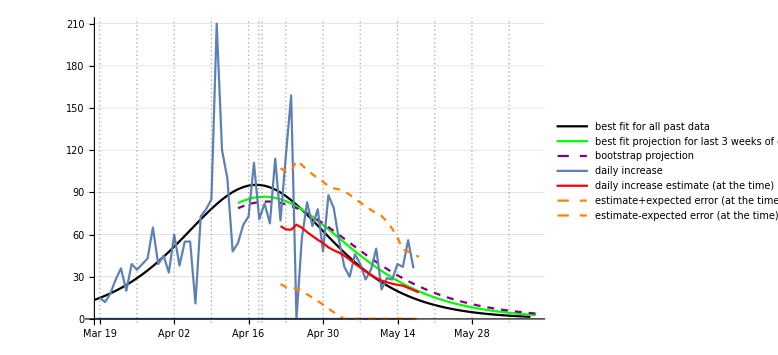

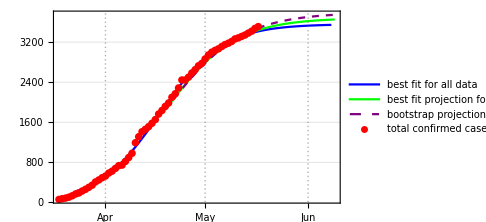

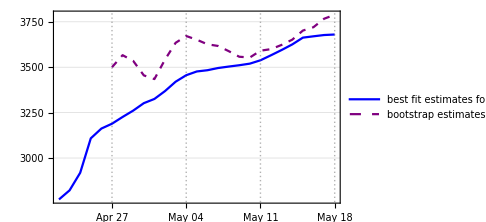

May 17

Hungarydate.txt

Hungarygraf.png

Hungaryloggraf.png

Hungarydfgraf.png

Hungaryfinalplot.png

country : France

data length : 74

start date : {2020,3,5}

jdp0 : {178501.,1594.92,0.136173}

jp20 : {180178.,6473.02,0.105977}

backward result : {99959.4,719.763,0.184535}

forward result : {180178.,6473.02,0.105977}

last tab: {180178.,6473.02,0.105977}

backward result : {99959.4,719.763,0.184535}

forward result : {180178.,6473.02,0.105977}

past errors : {{5503.77,6272.56,6874.53,6846.44,6886.25},6476.71}

boot tab : {{466817.,3627.78,0.0961974},{623845.,3965.63,0.0918199},{541701.,3956.86,0.0925342},{929276.,4392.58,0.0872302},{437666.,3997.64,0.0934772},{269683.,3171.06,0.105602},{230306.,2748.68,0.112725},{209435.,2407.76,0.118914},{188261.,1951.37,0.128306},{172978.,1531.93,0.138674},{171732.,1465.56,0.140375},{169586.,1371.41,0.142959},{168962.,1324.89,0.144202},{167687.,1256.69,0.146165},{171322.,1359.05,0.142854},{174502.,1465.48,0.139793},{172593.,1338.94,0.142927},{172737.,1294.7,0.143809},{172403.,1214.68,0.145659},{172274.,1128.22,0.147663},{171457.,1013.05,0.150822},{171532.,934.821,0.152865},{171728.,814.793,0.156265},{173497.,778.302,0.156505},{174032.,692.769,0.159103},{174820.,613.021,0.161652},{175269.,515.617,0.165584},{175737.,459.068,0.168073},{175998.,409.329,0.170617},{176584.,419.23,0.169601},{176941.,475.133,0.166385},{178355.,880.675,0.151065},{180902.,2749.83,0.123583},{185638.,12573.8,0.086995},{186991.,17501.8,0.0788539}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74}

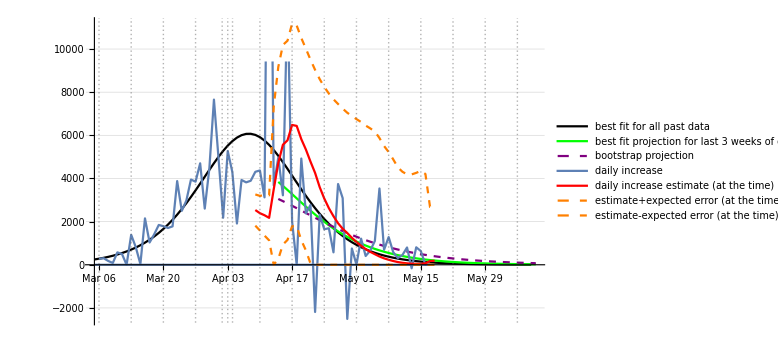

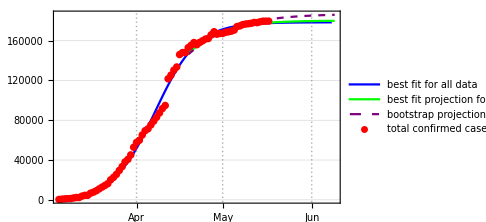

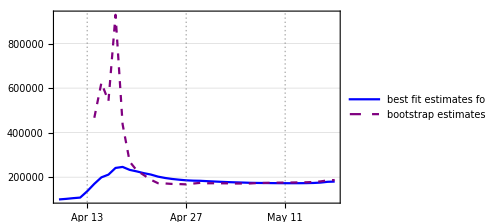

May 17

Francedate.txt

Francegraf.png

Franceloggraf.png

Francedfgraf.png

Francefinalplot.png

country : Singapore

data length : 48

start date : {2020,3,31}

jdp0 : {29251.1,714.969,0.12579}

jp20 : {36016.4,1983.08,0.0844302}

backward result : {25787.1,368.544,0.161986}

forward result : {36016.4,1983.08,0.0844302}

last tab: {36016.4,1983.08,0.0844302}

backward result : {25787.1,368.544,0.161986}

forward result : {36016.4,1983.08,0.0844302}

past errors : {{1429.91,1895.36,2432.57,2669.84,3149.57},2315.45}

boot tab : {{18609.7,185.163,0.206979},{19843.4,225.079,0.194109},{20798.2,259.355,0.184972},{21901.1,305.638,0.174815},{22991.7,359.902,0.165125},{24335.4,433.925,0.154339},{25866.,529.876,0.143264},{27652.9,655.403,0.131943},{30184.6,842.18,0.118987},{31527.8,979.632,0.1119},{34393.9,1232.6,0.100938},{37062.2,1502.7,0.0920415},{40493.3,1831.63,0.0832682},{44942.5,2233.67,0.0746694},{47266.3,2541.9,0.0697135},{51572.5,2973.41,0.0634869}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48}

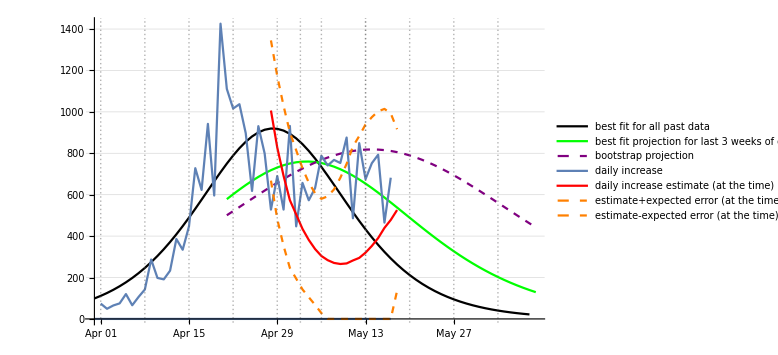

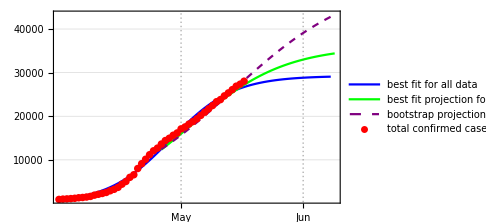

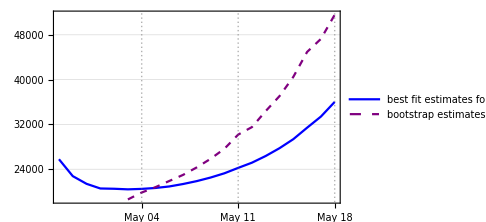

May 17

Singaporedate.txt

Singaporegraf.png

Singaporeloggraf.png

Singaporedfgraf.png

Singaporefinalplot.png

country : Serbia

data length : 63

start date : {2020,3,16}

jdp0 : {10527.9,134.672,0.133785}

jp20 : {10909.4,323.877,0.108119}

backward result : {5385.66,54.3172,0.189435}

forward result : {10909.4,323.877,0.108119}

last tab: {10909.4,323.877,0.108119}

backward result : {5385.66,54.3172,0.189435}

forward result : {10909.4,323.877,0.108119}

past errors : {{-9.80994,17.4397,34.7603,50.696,126.824},43.9819}

boot tab : {{16237.3,136.155,0.127234},{14766.,135.091,0.128497},{13037.6,129.209,0.131834},{11633.5,120.65,0.136346},{10300.6,106.533,0.143652},{9589.26,95.3574,0.149718},{9042.4,84.4661,0.156122},{8874.7,80.2651,0.158719},{8985.22,82.0488,0.157445},{9179.72,87.1824,0.15443},{9407.14,95.3318,0.150339},{9757.29,109.628,0.144118},{10135.6,127.484,0.137592},{10634.8,156.069,0.129184},{10435.4,148.668,0.131498},{10943.2,184.538,0.12282},{10956.4,190.843,0.121753},{10887.9,188.83,0.122336},{10794.2,183.387,0.123588},{10864.7,193.177,0.121759},{10730.2,184.86,0.123704},{10726.5,192.891,0.12258},{10776.2,212.194,0.119746},{10724.9,223.002,0.11883},{10859.5,270.301,0.112978},{10915.4,305.799,0.109497},{10929.8,330.509,0.107487},{10952.1,348.518,0.106025},{10970.9,358.356,0.105206},{10961.9,356.546,0.105399},{11045.1,394.201,0.102306}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63}

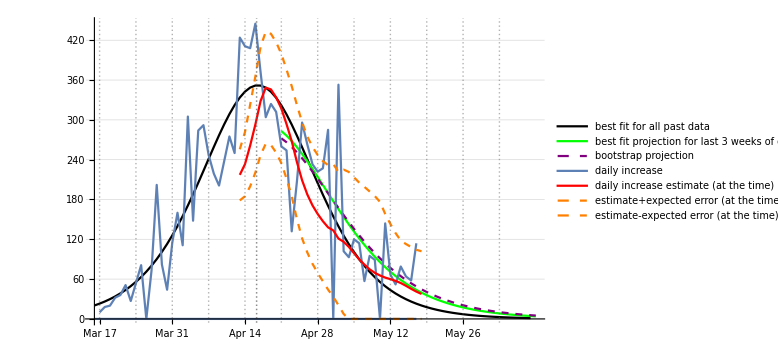

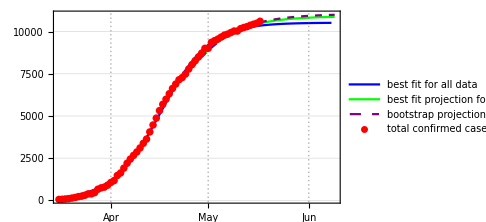

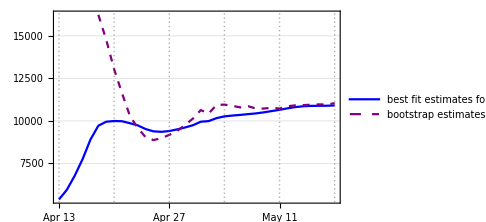

May 17

Serbiadate.txt

Serbiagraf.png

Serbialoggraf.png

Serbiadfgraf.png

Serbiafinalplot.png

country : Poland

data length : 66

start date : {2020,3,13}

jdp0 : {19234.4,547.711,0.0886038}

jp20 : {25630.5,1632.81,0.0547908}

backward result : {9497.75,130.037,0.165803}

forward result : {25630.5,1632.81,0.0547908}

last tab: {25630.5,1632.81,0.0547908}

backward result : {9497.75,130.037,0.165803}

forward result : {25630.5,1632.81,0.0547908}

past errors : {{510.222,695.915,881.183,915.915,990.969},798.841}

boot tab : {{13883.3,266.738,0.123333},{14122.8,280.713,0.120911},{14431.4,297.377,0.118154},{14637.5,313.401,0.115824},{15026.4,336.433,0.112541},{15494.6,363.965,0.10894},{15805.1,387.708,0.106245},{16187.3,416.08,0.103239},{16910.4,461.965,0.0986529},{17017.9,484.377,0.0969958},{17040.7,504.337,0.095731},{17206.8,531.802,0.0938598},{17548.9,572.267,0.0911189},{17834.4,615.529,0.0885433},{18685.9,701.534,0.0834997},{19430.4,788.366,0.0792242},{20229.5,880.935,0.07519},{21024.7,972.45,0.0716298},{21724.6,1066.58,0.0684798},{22427.1,1158.27,0.0656657},{23147.9,1257.16,0.0629412},{25942.9,1491.87,0.0565531},{27183.9,1619.11,0.0538202},{29744.1,1811.52,0.0498462},{32899.3,2011.33,0.0461654},{33429.9,2087.47,0.0451559},{32673.,2110.08,0.0452058}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66}

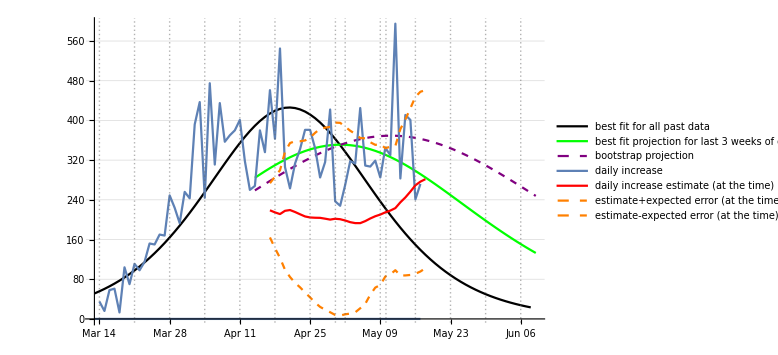

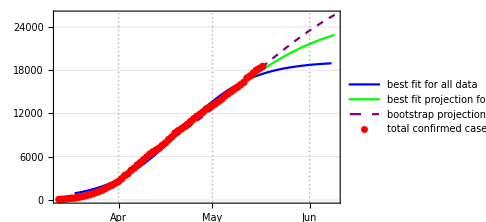

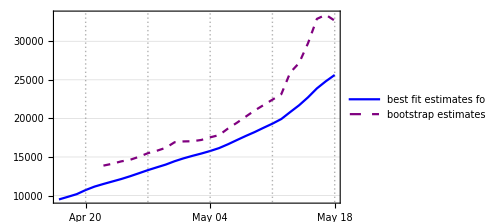

May 17

Polanddate.txt

Polandgraf.png

Polandloggraf.png

Polanddfgraf.png

Polandfinalplot.png

{104.4529,Null}

```mathematica
countrydateplotlist={};
Timing[
For[cit=1,cit≤Length[countryparameters],cit++,
countrynames=Transpose[countryparameters][[1]];
currentnamme=countrynames[[cit]];
{currentnamme,ctrunc,jdp0,jlag,jprojtime,jbootlag,jplotdrop}=countryparameters[[cit]];
Print["country : ",currentnamme];
countinds=Flatten[Position[countriescsv,currentnamme]];
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}];

truncdatesandata=Select[datesanddata,#[[2]]>ctrunc&];
justdata=Transpose[truncdatesandata][[2]];
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]];
Print["data length : ",Length[justdata]];
Print["start date : ",jstartdate];

{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime];
Print["jdp0 : ",jdp0];
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,jlag,justtime,{1,0}];
Print["jp20 : ",jp20];

(*update jdp0*)
countryparameters[[cit,3]]=jdp0;

{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,jbootabc}=somegraphs2[jdp0,jp20,justtime,justdata,jstartdate,jlag,jprojtime,5,jbootlag,wpopulations[[cit]]];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]-1];
Print[jgraf];
Print[jloggraf];
Print[jfinal];

(*jdatestring=reldatetostring[cpstartdate,timecpert[[-1]]];*)

Print[jdatestring];

If[jp20[[1]]10^5/wpopulations[[cit]]>grafthreshhold,
morecountrynames=AppendTo[morecountrynames,currentnamme],
lesscountrynames=AppendTo[lesscountrynames,currentnamme]
];

(*new zealand string exception*)
If[currentnamme==="New Zealand",currentnamme="newzealand"];
(*uk  string exception*)
If[currentnamme==="United Kingdom",currentnamme="uk"];


datefilename=currentnamme<>"date.txt";
Print[datefilename];
Export[datefilename,jdatestring];
graffilename=currentnamme<>"graf.png";
Export[graffilename,jgraf];
Print[graffilename];
loggraffilename=currentnamme<>"loggraf.png";
Export[loggraffilename,jloggraf];
Print[loggraffilename];
dfgraffilename=currentnamme<>"dfgraf.png";
Export[dfgraffilename,jdfpplot];
Print[dfgraffilename];
finalgraffilename=currentnamme<>"finalplot.png";
Export[finalgraffilename,jfinal];
Print[finalgraffilename];

drcases=Transpose[datesanddata][[2]];
drcases=drcases/wpopulations[[cit]];
datesanddata=Transpose[{Transpose[datesanddata][[1]],drcases}];
countrydateplotlist=AppendTo[countrydateplotlist,datesanddata];
]
]
```

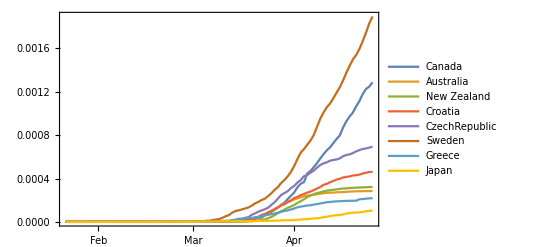

```mathematica
DateListPlot[countrydateplotlist,PlotLegends->wolfcountrynames,PlotRange->All]
```

```mathematica
allcountrynames=Join[fwcountrynames,wolfcountrynames]
%//Length
Length[countrybootabcs]
```

{Slovenia,Italy,Austria,Germany,USA,Canada,Australia,New Zealand,Croatia,CzechRepublic,Singapore,Japan}

12

12

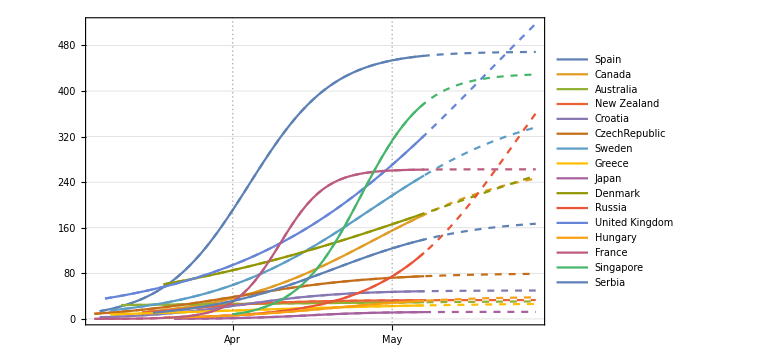

```mathematica
projfwcountryplot=DateListPlot[countrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,countrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->wolfcountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

```mathematica
countrybootabcs//Length
morecountrybootabcs//Length
lesscountrybootabcs//Length
morecountrynames
lesscountrynames
```

17

9

8

{Spain,Canada,Sweden,Denmark,Russia,United Kingdom,France,Singapore,Serbia}

{Australia,New Zealand,Croatia,Czechia,Greece,Japan,Hungary,Poland}

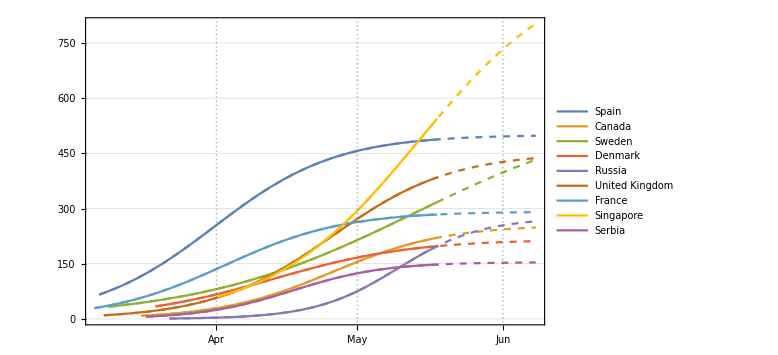

```mathematica
projfwcountryplot=DateListPlot[morecountrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,morecountrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->morecountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["moremscprojplots.png",mscprojplots]
```

moremscprojplots.png

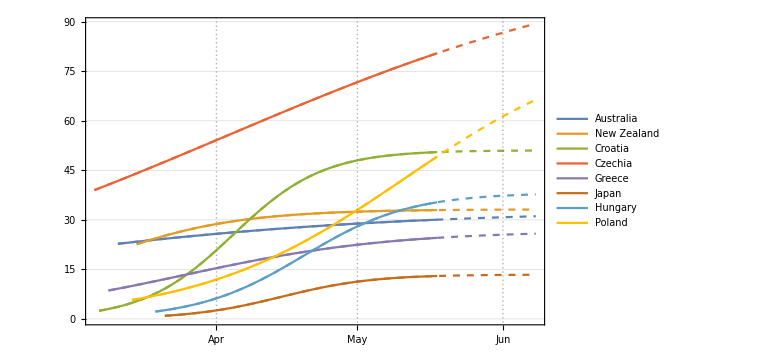

```mathematica
projfwcountryplot=DateListPlot[lesscountrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,lesscountrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->lesscountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["lessmscprojplots.png",mscprojplots]
```

lessmscprojplots.png

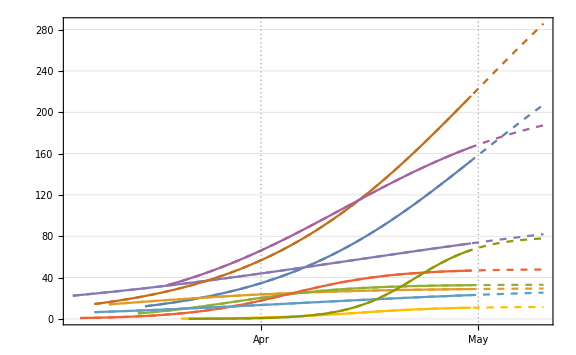
```mathematica
29.4.
-Graphics-
```

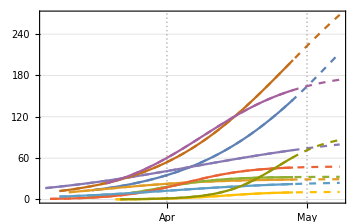
```mathematica
28.4.
-Graphics-
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

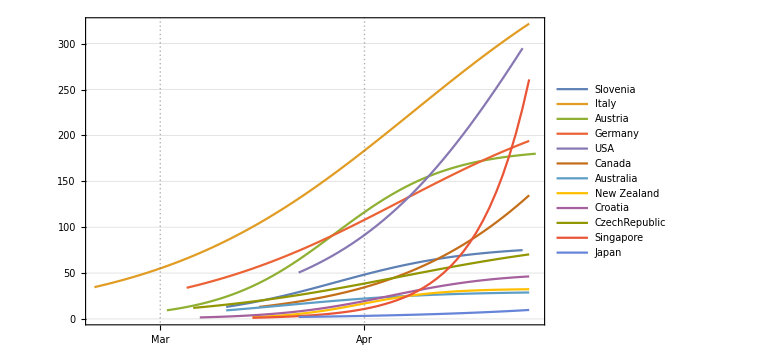

```mathematica
DateListPlot[countrybootabcs,PlotRange->All,PlotLegends->allcountrynames,ImageSize->Large,PlotTheme->"Detailed"]
```

```mathematica
ColorData
```

```mathematica
countinds=Flatten[Position[countriescsv,"Poland"]]
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}]
```

{185}

{{{2020,1,22},0},{{2020,1,23},0},{{2020,1,24},0},{{2020,1,25},0},{{2020,1,26},0},{{2020,1,27},0},{{2020,1,28},0},{{2020,1,29},0},{{2020,1,30},0},{{2020,1,31},0},{{2020,2,1},0},{{2020,2,2},0},{{2020,2,3},0},{{2020,2,4},0},{{2020,2,5},0},{{2020,2,6},0},{{2020,2,7},0},{{2020,2,8},0},{{2020,2,9},0},{{2020,2,10},0},{{2020,2,11},0},{{2020,2,12},0},{{2020,2,13},0},{{2020,2,14},0},{{2020,2,15},0},{{2020,2,16},0},{{2020,2,17},0},{{2020,2,18},0},{{2020,2,19},0},{{2020,2,20},0},{{2020,2,21},0},{{2020,2,22},0},{{2020,2,23},0},{{2020,2,24},0},{{2020,2,25},0},{{2020,2,26},0},{{2020,2,27},0},{{2020,2,28},0},{{2020,2,29},0},{{2020,3,1},0},{{2020,3,2},0},{{2020,3,3},0},{{2020,3,4},1},{{2020,3,5},1},{{2020,3,6},5},{{2020,3,7},5},{{2020,3,8},11},{{2020,3,9},16},{{2020,3,10},22},{{2020,3,11},31},{{2020,3,12},49},{{2020,3,13},68},{{2020,3,14},103},{{2020,3,15},119},{{2020,3,16},177},{{2020,3,17},238},{{2020,3,18},251},{{2020,3,19},355},{{2020,3,20},425},{{2020,3,21},536},{{2020,3,22},634},{{2020,3,23},749},{{2020,3,24},901},{{2020,3,25},1051},{{2020,3,26},1221},{{2020,3,27},1389},{{2020,3,28},1638},{{2020,3,29},1862},{{2020,3,30},2055},{{2020,3,31},2311},{{2020,4,1},2554},{{2020,4,2},2946},{{2020,4,3},3383},{{2020,4,4},3627},{{2020,4,5},4102},{{2020,4,6},4413},{{2020,4,7},4848},{{2020,4,8},5205},{{2020,4,9},5575},{{2020,4,10},5955},{{2020,4,11},6356},{{2020,4,12},6674},{{2020,4,13},6934},{{2020,4,14},7202},{{2020,4,15},7582},{{2020,4,16},7918},{{2020,4,17},8379},{{2020,4,18},8742},{{2020,4,19},9287},{{2020,4,20},9593},{{2020,4,21},9856},{{2020,4,22},10169},{{2020,4,23},10511},{{2020,4,24},10892},{{2020,4,25},11273},{{2020,4,26},11617},{{2020,4,27},11902},{{2020,4,28},12218},{{2020,4,29},12640},{{2020,4,30},12877},{{2020,5,1},13105},{{2020,5,2},13375},{{2020,5,3},13693},{{2020,5,4},14006},{{2020,5,5},14431},{{2020,5,6},14740},{{2020,5,7},15047},{{2020,5,8},15366}}

```mathematica
truncdatesandata=Select[datesanddata,#[[2]]>50&]
%//Length
justdata=Transpose[truncdatesandata][[2]]
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]]
```

{{{2020,3,13},68},{{2020,3,14},103},{{2020,3,15},119},{{2020,3,16},177},{{2020,3,17},238},{{2020,3,18},251},{{2020,3,19},355},{{2020,3,20},425},{{2020,3,21},536},{{2020,3,22},634},{{2020,3,23},749},{{2020,3,24},901},{{2020,3,25},1051},{{2020,3,26},1221},{{2020,3,27},1389},{{2020,3,28},1638},{{2020,3,29},1862},{{2020,3,30},2055},{{2020,3,31},2311},{{2020,4,1},2554},{{2020,4,2},2946},{{2020,4,3},3383},{{2020,4,4},3627},{{2020,4,5},4102},{{2020,4,6},4413},{{2020,4,7},4848},{{2020,4,8},5205},{{2020,4,9},5575},{{2020,4,10},5955},{{2020,4,11},6356},{{2020,4,12},6674},{{2020,4,13},6934},{{2020,4,14},7202},{{2020,4,15},7582},{{2020,4,16},7918},{{2020,4,17},8379},{{2020,4,18},8742},{{2020,4,19},9287},{{2020,4,20},9593},{{2020,4,21},9856},{{2020,4,22},10169},{{2020,4,23},10511},{{2020,4,24},10892},{{2020,4,25},11273},{{2020,4,26},11617},{{2020,4,27},11902},{{2020,4,28},12218},{{2020,4,29},12640},{{2020,4,30},12877},{{2020,5,1},13105},{{2020,5,2},13375},{{2020,5,3},13693},{{2020,5,4},14006},{{2020,5,5},14431},{{2020,5,6},14740},{{2020,5,7},15047},{{2020,5,8},15366}}

57

{68,103,119,177,238,251,355,425,536,634,749,901,1051,1221,1389,1638,1862,2055,2311,2554,2946,3383,3627,4102,4413,4848,5205,5575,5955,6356,6674,6934,7202,7582,7918,8379,8742,9287,9593,9856,10169,10511,10892,11273,11617,11902,12218,12640,12877,13105,13375,13693,14006,14431,14740,15047,15366}

{2020,3,13}

```mathematica
jdp0={Max[justdata]1.5,150,0.12}
```

{23049.,150,0.12}

```mathematica
jdp0={2.835279843883035*^8,64.38918662693713,0.1259411788554341}
```

{2.83528×10^8,64.3892,0.125941}

```mathematica
jdp0={1.1513551375078703*^6,30102.77946079763,0.1242005827138709}
```

{1.15136×10^6,30102.8,0.124201}

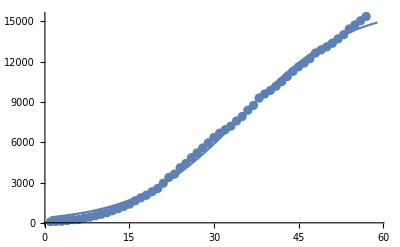

```mathematica
showplots[justdata,jdp0,justtime]
```

```mathematica
{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime]
```

{{16098.4,370.628,0.106508},14,2.69826×10^-8,57}

{19509.6,978.105,0.0737384}

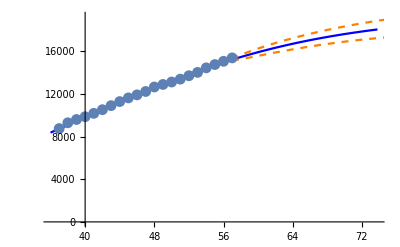
{-Graphics-,242.344,98.9939,319,-17.1075,78.7611}

```mathematica
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,28,justtime,{1,0}];
jp20
jpdata20=justdata[[-21;;]];
datastats[jpdata20,jp20,1.8,2,justtime[[-21;;]]]
```

```mathematica
estimates[justdata,jdp0,21,justtime];
```

backward result : {5109.3,89.9793,0.203261}

forward result : {21779.4,1446.22,0.0613938}

```mathematica
TableView[Transpose[generatestats[justdata,jdp0,28,justtime,jstartdate]]];
```

{981.19,4.49853,0.341492}

{1452.18,18.7219,0.227054}

{1452.18,18.7219,0.227054}

```mathematica
{"Russia",300,{133764.28972174952,345.7178233894532,0.17211220984196077},21,14,10,0}
```

```mathematica
{"Japan",950,{17986.663577976567,576.9474735585374,0.12382285884487645},21,14,8,0}
```

```mathematica
{name,trunc,cp0,lag,projt,bootl,drop}
```

```mathematica
{"Sweden",200,{23138.83457722449,461.922977379802,0.10293773671900139},28,14,10,0}
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0}
```

```mathematica
{"Denmark",1100,{9249.181828199724,848.3550476707888,0.11809736637519559},28,14,10,0}
```

```mathematica
{"Greece",50,{2469.7252428688025,97.9216579531985,0.1381653045706424},21,14,10,0}
```

{Greece,50,{2469.73,97.9217,0.138165},21,14,10,0}

```mathematica
{"United Kingdom",200,{181106.79697173668,1069.9501757425367,0.1337539999625829},21,14,10,0}
{"Hungary",50,{3365.6444625267736,104.40659882066325,0.11408451894205024},28,14,10,0}
{"France",50,{177276.3912847858,1518.766119969371,0.13797898997605668},28,14,10,0}
{"Singapore",900,{21078.466173566427,299.80354836134035,0.17802870984146776},28,14,5,0}
{"Serbia",50,{10139.282988917936,113.99752601777078,0.1410478828462318},21,14,10,0}
{"Poland",50,{16098.415437312473,370.62817701093553,0.1065084233501309},21,14,10,0}
```

backward result : {5109.3,89.9793,0.203261}

forward result : {21779.4,1446.22,0.0613938}

last tab: {21779.4,1446.22,0.0613938}

backward result : {5109.3,89.9793,0.203261}

forward result : {21779.4,1446.22,0.0613938}

past errors : {{117.158,64.109,13.5794,16.8407,80.06,150.308,344.565,434.733,534.641,658.056},241.405}

boot tab : {{13627.2,229.936,0.131347},{11114.3,195.435,0.142952},{10824.6,192.529,0.144397},{10136.9,166.727,0.152786},{10413.6,178.982,0.14892},{10892.5,200.413,0.142841},{11475.1,232.693,0.1352},{13056.1,314.746,0.119793},{14215.8,393.753,0.109384},{15056.2,469.13,0.101855},{16576.3,584.856,0.0922481},{18811.3,722.096,0.0829107},{21650.4,856.053,0.0752707},{25305.2,1013.54,0.0680646},{28097.1,1131.12,0.063654},{28821.6,1227.54,0.0610384},{28616.2,1291.62,0.0596942},{28461.2,1361.97,0.0582909},{25710.5,1350.59,0.0598001},{23260.5,1284.86,0.0627113},{21267.1,1166.66,0.0670085},{20420.5,1097.63,0.0695436},{20210.8,1097.91,0.0698218},{20915.,1215.07,0.0664652},{21692.,1365.15,0.0627461},{23200.1,1614.66,0.0572315},{25449.5,1913.16,0.0514437}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57}

May 09

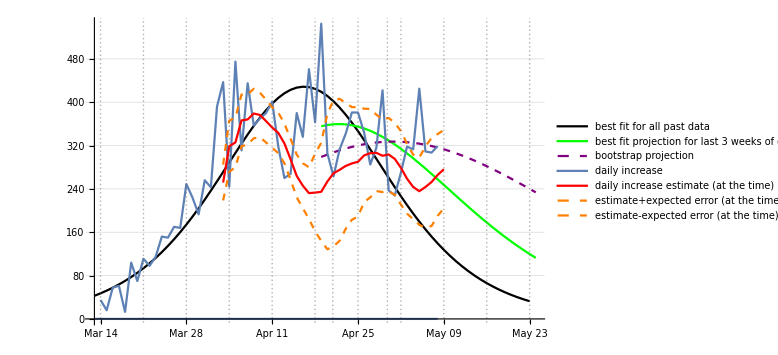

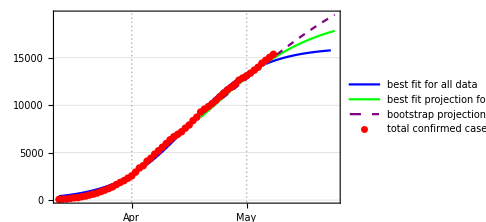

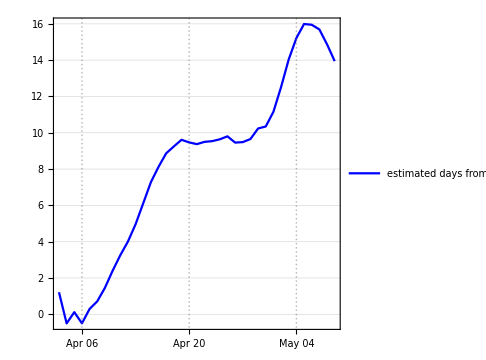

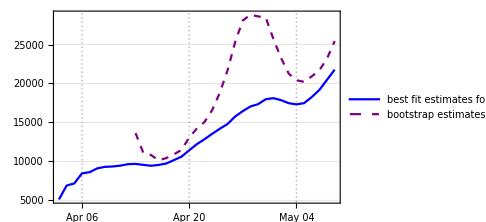

```mathematica
{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,cboo}=somegraphs2[jdp0,jp20,justtime,justdata,jstartdate,21,14,0,10,1000];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]]
jgraf
jloggraf
jdfpplot
jfinal
```